the rules of chess occupy 10 to the 5 pages in this language.

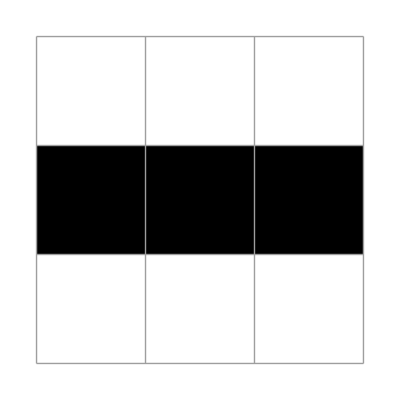
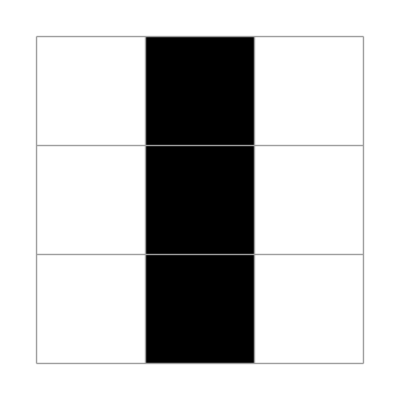

-Graphics-

```mathematica
X1=({{0, 0, 0}, {1, 1, 1}, {0, 0, 0}});
plt/@NestList[updateLife[{3,3}][ #]&,
X1,1]
```

```mathematica
Binomial[8,4]
```

70

```mathematica
Not/@Prepend[{1,2,3,4} ,xP]
```

{!xP,!1,!2,!3,!4}

## the 70

```mathematica
lifeNeighbours={xNW,xN,xNE,xW,xE,xSW,xS,xSE};
lists70=(Not/@Prepend[#,xP])&/@Subsets[lifeNeighbours,{4}];
the70=And@@Or@@@lists70;
the70
```

(!xP||!xNW||!xN||!xNE||!xW)&&(!xP||!xNW||!xN||!xNE||!xE)&&(!xP||!xNW||!xN||!xNE||!xSW)&&(!xP||!xNW||!xN||!xNE||!xS)&&(!xP||!xNW||!xN||!xNE||!xSE)&&(!xP||!xNW||!xN||!xW||!xE)&&(!xP||!xNW||!xN||!xW||!xSW)&&(!xP||!xNW||!xN||!xW||!xS)&&(!xP||!xNW||!xN||!xW||!xSE)&&(!xP||!xNW||!xN||!xE||!xSW)&&(!xP||!xNW||!xN||!xE||!xS)&&(!xP||!xNW||!xN||!xE||!xSE)&&(!xP||!xNW||!xN||!xSW||!xS)&&(!xP||!xNW||!xN||!xSW||!xSE)&&(!xP||!xNW||!xN||!xS||!xSE)&&(!xP||!xNW||!xNE||!xW||!xE)&&(!xP||!xNW||!xNE||!xW||!xSW)&&(!xP||!xNW||!xNE||!xW||!xS)&&(!xP||!xNW||!xNE||!xW||!xSE)&&(!xP||!xNW||!xNE||!xE||!xSW)&&(!xP||!xNW||!xNE||!xE||!xS)&&(!xP||!xNW||!xNE||!xE||!xSE)&&(!xP||!xNW||!xNE||!xSW||!xS)&&(!xP||!xNW||!xNE||!xSW||!xSE)&&(!xP||!xNW||!xNE||!xS||!xSE)&&(!xP||!xNW||!xW||!xE||!xSW)&&(!xP||!xNW||!xW||!xE||!xS)&&(!xP||!xNW||!xW||!xE||!xSE)&&(!xP||!xNW||!xW||!xSW||!xS)&&(!xP||!xNW||!xW||!xSW||!xSE)&&(!xP||!xNW||!xW||!xS||!xSE)&&(!xP||!xNW||!xE||!xSW||!xS)&&(!xP||!xNW||!xE||!xSW||!xSE)&&(!xP||!xNW||!xE||!xS||!xSE)&&(!xP||!xNW||!xSW||!xS||!xSE)&&(!xP||!xN||!xNE||!xW||!xE)&&(!xP||!xN||!xNE||!xW||!xSW)&&(!xP||!xN||!xNE||!xW||!xS)&&(!xP||!xN||!xNE||!xW||!xSE)&&(!xP||!xN||!xNE||!xE||!xSW)&&(!xP||!xN||!xNE||!xE||!xS)&&(!xP||!xN||!xNE||!xE||!xSE)&&(!xP||!xN||!xNE||!xSW||!xS)&&(!xP||!xN||!xNE||!xSW||!xSE)&&(!xP||!xN||!xNE||!xS||!xSE)&&(!xP||!xN||!xW||!xE||!xSW)&&(!xP||!xN||!xW||!xE||!xS)&&(!xP||!xN||!xW||!xE||!xSE)&&(!xP||!xN||!xW||!xSW||!xS)&&(!xP||!xN||!xW||!xSW||!xSE)&&(!xP||!xN||!xW||!xS||!xSE)&&(!xP||!xN||!xE||!xSW||!xS)&&(!xP||!xN||!xE||!xSW||!xSE)&&(!xP||!xN||!xE||!xS||!xSE)&&(!xP||!xN||!xSW||!xS||!xSE)&&(!xP||!xNE||!xW||!xE||!xSW)&&(!xP||!xNE||!xW||!xE||!xS)&&(!xP||!xNE||!xW||!xE||!xSE)&&(!xP||!xNE||!xW||!xSW||!xS)&&(!xP||!xNE||!xW||!xSW||!xSE)&&(!xP||!xNE||!xW||!xS||!xSE)&&(!xP||!xNE||!xE||!xSW||!xS)&&(!xP||!xNE||!xE||!xSW||!xSE)&&(!xP||!xNE||!xE||!xS||!xSE)&&(!xP||!xNE||!xSW||!xS||!xSE)&&(!xP||!xW||!xE||!xSW||!xS)&&(!xP||!xW||!xE||!xSW||!xSE)&&(!xP||!xW||!xE||!xS||!xSE)&&(!xP||!xW||!xSW||!xS||!xSE)&&(!xP||!xE||!xSW||!xS||!xSE)

(¬xP∨¬xNW∨¬xN∨¬xNE∨¬xW)∧(¬xP∨¬xNW∨¬xN∨¬xNE∨¬xE)∧(¬xP∨¬xNW∨¬xN∨¬xNE∨¬xSW)∧(¬xP∨¬xNW∨¬xN∨¬xNE∨¬xS)∧(¬xP∨¬xNW∨¬xN∨¬xNE∨¬xSE)∧(¬xP∨¬xNW∨¬xN∨¬xW∨¬xE)∧(¬xP∨¬xNW∨¬xN∨¬xW∨¬xSW)∧(¬xP∨¬xNW∨¬xN∨¬xW∨¬xS)∧(¬xP∨¬xNW∨¬xN∨¬xW∨¬xSE)∧(¬xP∨¬xNW∨¬xN∨¬xE∨¬xSW)∧(¬xP∨¬xNW∨¬xN∨¬xE∨¬xS)∧(¬xP∨¬xNW∨¬xN∨¬xE∨¬xSE)∧(¬xP∨¬xNW∨¬xN∨¬xSW∨¬xS)∧(¬xP∨¬xNW∨¬xN∨¬xSW∨¬xSE)∧(¬xP∨¬xNW∨¬xN∨¬xS∨¬xSE)∧(¬xP∨¬xNW∨¬xNE∨¬xW∨¬xE)∧(¬xP∨¬xNW∨¬xNE∨¬xW∨¬xSW)∧(¬xP∨¬xNW∨¬xNE∨¬xW∨¬xS)∧(¬xP∨¬xNW∨¬xNE∨¬xW∨¬xSE)∧(¬xP∨¬xNW∨¬xNE∨¬xE∨¬xSW)∧(¬xP∨¬xNW∨¬xNE∨¬xE∨¬xS)∧(¬xP∨¬xNW∨¬xNE∨¬xE∨¬xSE)∧(¬xP∨¬xNW∨¬xNE∨¬xSW∨¬xS)∧(¬xP∨¬xNW∨¬xNE∨¬xSW∨¬xSE)∧(¬xP∨¬xNW∨¬xNE∨¬xS∨¬xSE)∧(¬xP∨¬xNW∨¬xW∨¬xE∨¬xSW)∧(¬xP∨¬xNW∨¬xW∨¬xE∨¬xS)∧(¬xP∨¬xNW∨¬xW∨¬xE∨¬xSE)∧(¬xP∨¬xNW∨¬xW∨¬xSW∨¬xS)∧(¬xP∨¬xNW∨¬xW∨¬xSW∨¬xSE)∧(¬xP∨¬xNW∨¬xW∨¬xS∨¬xSE)∧(¬xP∨¬xNW∨¬xE∨¬xSW∨¬xS)∧(¬xP∨¬xNW∨¬xE∨¬xSW∨¬xSE)∧(¬xP∨¬xNW∨¬xE∨¬xS∨¬xSE)∧(¬xP∨¬xNW∨¬xSW∨¬xS∨¬xSE)∧(¬xP∨¬xN∨¬xNE∨¬xW∨¬xE)∧(¬xP∨¬xN∨¬xNE∨¬xW∨¬xSW)∧(¬xP∨¬xN∨¬xNE∨¬xW∨¬xS)∧(¬xP∨¬xN∨¬xNE∨¬xW∨¬xSE)∧(¬xP∨¬xN∨¬xNE∨¬xE∨¬xSW)∧(¬xP∨¬xN∨¬xNE∨¬xE∨¬xS)∧(¬xP∨¬xN∨¬xNE∨¬xE∨¬xSE)∧(¬xP∨¬xN∨¬xNE∨¬xSW∨¬xS)∧(¬xP∨¬xN∨¬xNE∨¬xSW∨¬xSE)∧(¬xP∨¬xN∨¬xNE∨¬xS∨¬xSE)∧(¬xP∨¬xN∨¬xW∨¬xE∨¬xSW)∧(¬xP∨¬xN∨¬xW∨¬xE∨¬xS)∧(¬xP∨¬xN∨¬xW∨¬xE∨¬xSE)∧(¬xP∨¬xN∨¬xW∨¬xSW∨¬xS)∧(¬xP∨¬xN∨¬xW∨¬xSW∨¬xSE)∧(¬xP∨¬xN∨¬xW∨¬xS∨¬xSE)∧(¬xP∨¬xN∨¬xE∨¬xSW∨¬xS)∧(¬xP∨¬xN∨¬xE∨¬xSW∨¬xSE)∧(¬xP∨¬xN∨¬xE∨¬xS∨¬xSE)∧(¬xP∨¬xN∨¬xSW∨¬xS∨¬xSE)∧(¬xP∨¬xNE∨¬xW∨¬xE∨¬xSW)∧(¬xP∨¬xNE∨¬xW∨¬xE∨¬xS)∧(¬xP∨¬xNE∨¬xW∨¬xE∨¬xSE)∧(¬xP∨¬xNE∨¬xW∨¬xSW∨¬xS)∧(¬xP∨¬xNE∨¬xW∨¬xSW∨¬xSE)∧(¬xP∨¬xNE∨¬xW∨¬xS∨¬xSE)∧(¬xP∨¬xNE∨¬xE∨¬xSW∨¬xS)∧(¬xP∨¬xNE∨¬xE∨¬xSW∨¬xSE)∧(¬xP∨¬xNE∨¬xE∨¬xS∨¬xSE)∧(¬xP∨¬xNE∨¬xSW∨¬xS∨¬xSE)∧(¬xP∨¬xW∨¬xE∨¬xSW∨¬xS)∧(¬xP∨¬xW∨¬xE∨¬xSW∨¬xSE)∧(¬xP∨¬xW∨¬xE∨¬xS∨¬xSE)∧(¬xP∨¬xW∨¬xSW∨¬xS∨¬xSE)∧(¬xP∨¬xE∨¬xSW∨¬xS∨¬xSE)